(m^2 ϕ^2)/2

m^2 ϕ

m^2

0

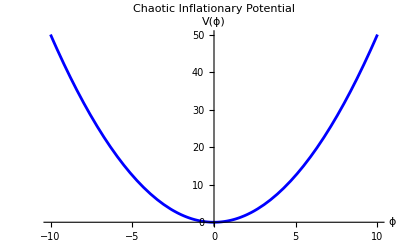

2/ϕ^2

2/ϕ^2

0

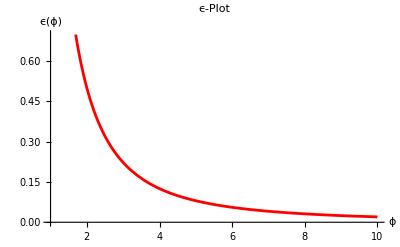

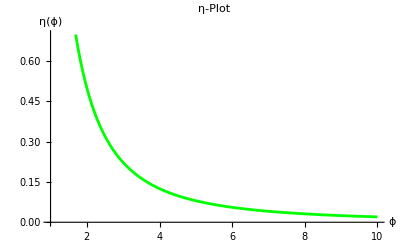

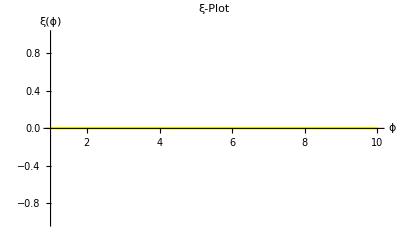

1-8/ϕ^2

-32/ϕ^4

32/ϕ^2

ϕ==60

```mathematica
ClearAll["Global`*"]
V[ϕ_,m_] = (1/2)m^2ϕ^2
dVdϕ[ϕ_,m_] = D[V[ϕ,m],ϕ]
d2Vdϕ2[ϕ_,m_] = D[dVdϕ[ϕ,m],ϕ]
d3Vdϕ3[ϕ_,m_]=D[d2Vdϕ2[ϕ,m],ϕ]

mValue = 1;
potentialPlot = Plot[V[ϕ,mValue],{ϕ,-10,10},
PlotLabel->"Chaotic Inflationary Potential",
AxesLabel->{"ϕ","V(ϕ)"},PlotStyle->Blue]

ϵ[ϕ_,m_] = (1/2) (dVdϕ[ϕ,m]/V[ϕ,m])^2
η[ϕ_,m_] =d2Vdϕ2[ϕ,m]/V[ϕ,m] 
ξ[ϕ_,m_]= (dVdϕ[ϕ,m]d3Vdϕ3[ϕ,m])/(V[ϕ,m])^2 


ϵPlot = Plot[ϵ[ϕ,mValue],{ϕ,1,10},
PlotLabel->"ϵ-Plot",
AxesLabel->{"ϕ","ϵ(ϕ)"},PlotStyle->Red]

ηPlot= Plot[η[ϕ,mValue],{ϕ,1,10},
PlotLabel->"η-Plot",
AxesLabel->{"ϕ","η(ϕ)"},PlotStyle->Green]

ξPlot=Plot[ξ[ϕ,mValue],{ϕ,1,10},
PlotLabel->"ξ-Plot",
AxesLabel->{"ϕ","ξ(ϕ)"},PlotStyle->Yellow]

Subscript[n, s]=1-6ϵ[ϕ,mValue]+2η[ϕ,mValue]
Subscript[α, s]=16ϵ[ϕ,mValue]η[ϕ,mValue]-24(ϵ[ϕ,mValue])^2-2ξ[ϕ,mValue]
r=16ϵ[ϕ,mValue]
```